```mathematica
<<HighEnergyPhysics`FeynCalc`
```

Loading FeynCalc from

FeynCalc 8.0.0.beta3 For help, type ?FeynCalc, use the built-in help system or visit www.feyncalc.org

Loading FeynArts, see www.feynarts.de for documentation

FeynArts 3.4 patched for use with FeynCalc

```mathematica
<<FeynArts`
```

FeynArts 3.4

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 3 Feb 09

patched for use with FeynCalc by Frederik Orellana and Rolf Mertig

```mathematica
t12=CreateTopologies[0,5];
```

```mathematica
AA=InsertFields[t12,{V[5],V[5],V[5],V[5],V[5]}->{},Model->"SMQCD",InsertionLevel->{Classes}]
```

TopologyList(Process→{V(5,{Glu1}),V(5,{Glu2}),V(5,{Glu3}),V(5,{Glu4}),V(5,{Glu5})}→{},Model→SMQCD,GenericModel→Lorentz,InsertionLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})«1»

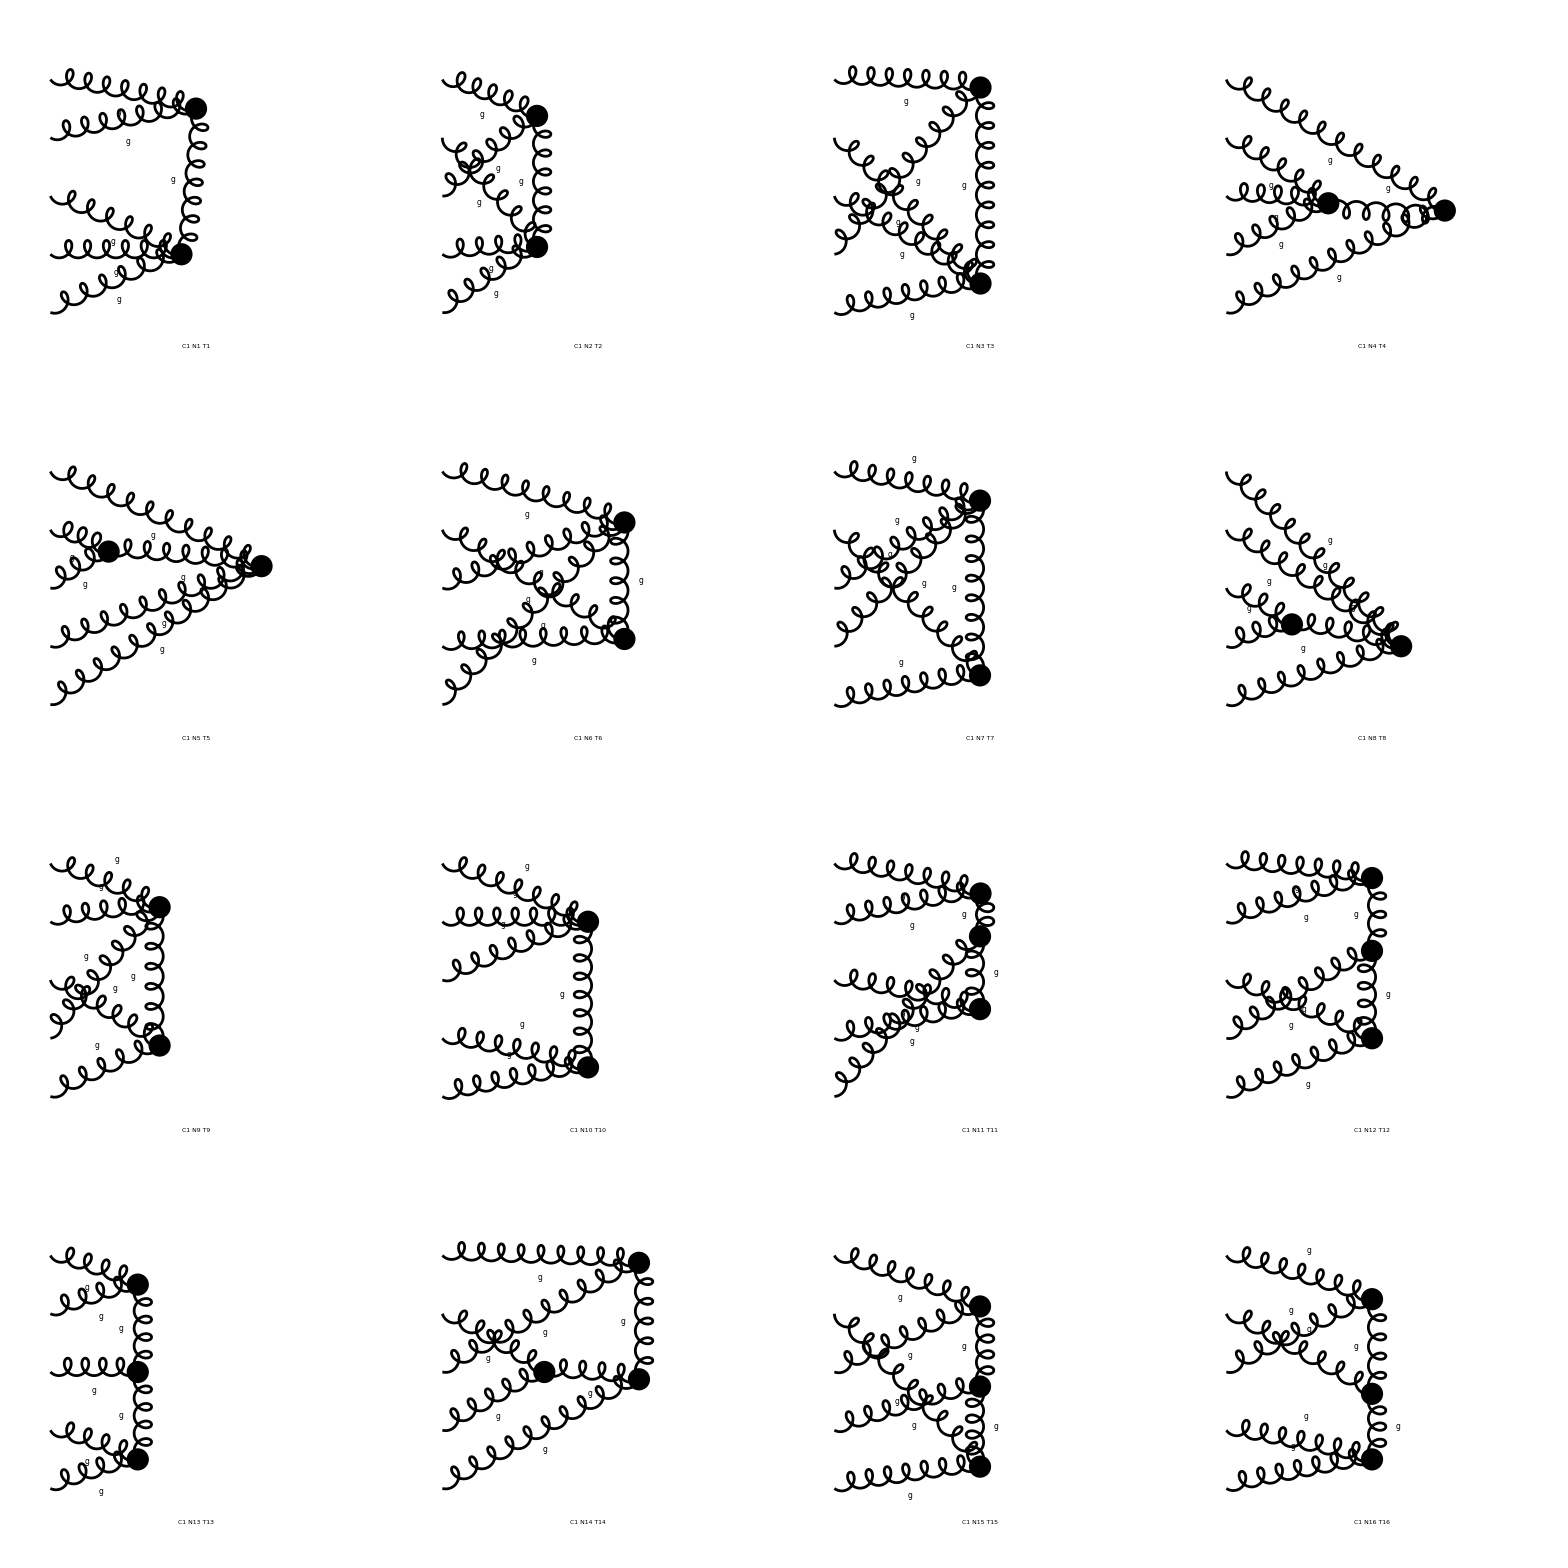

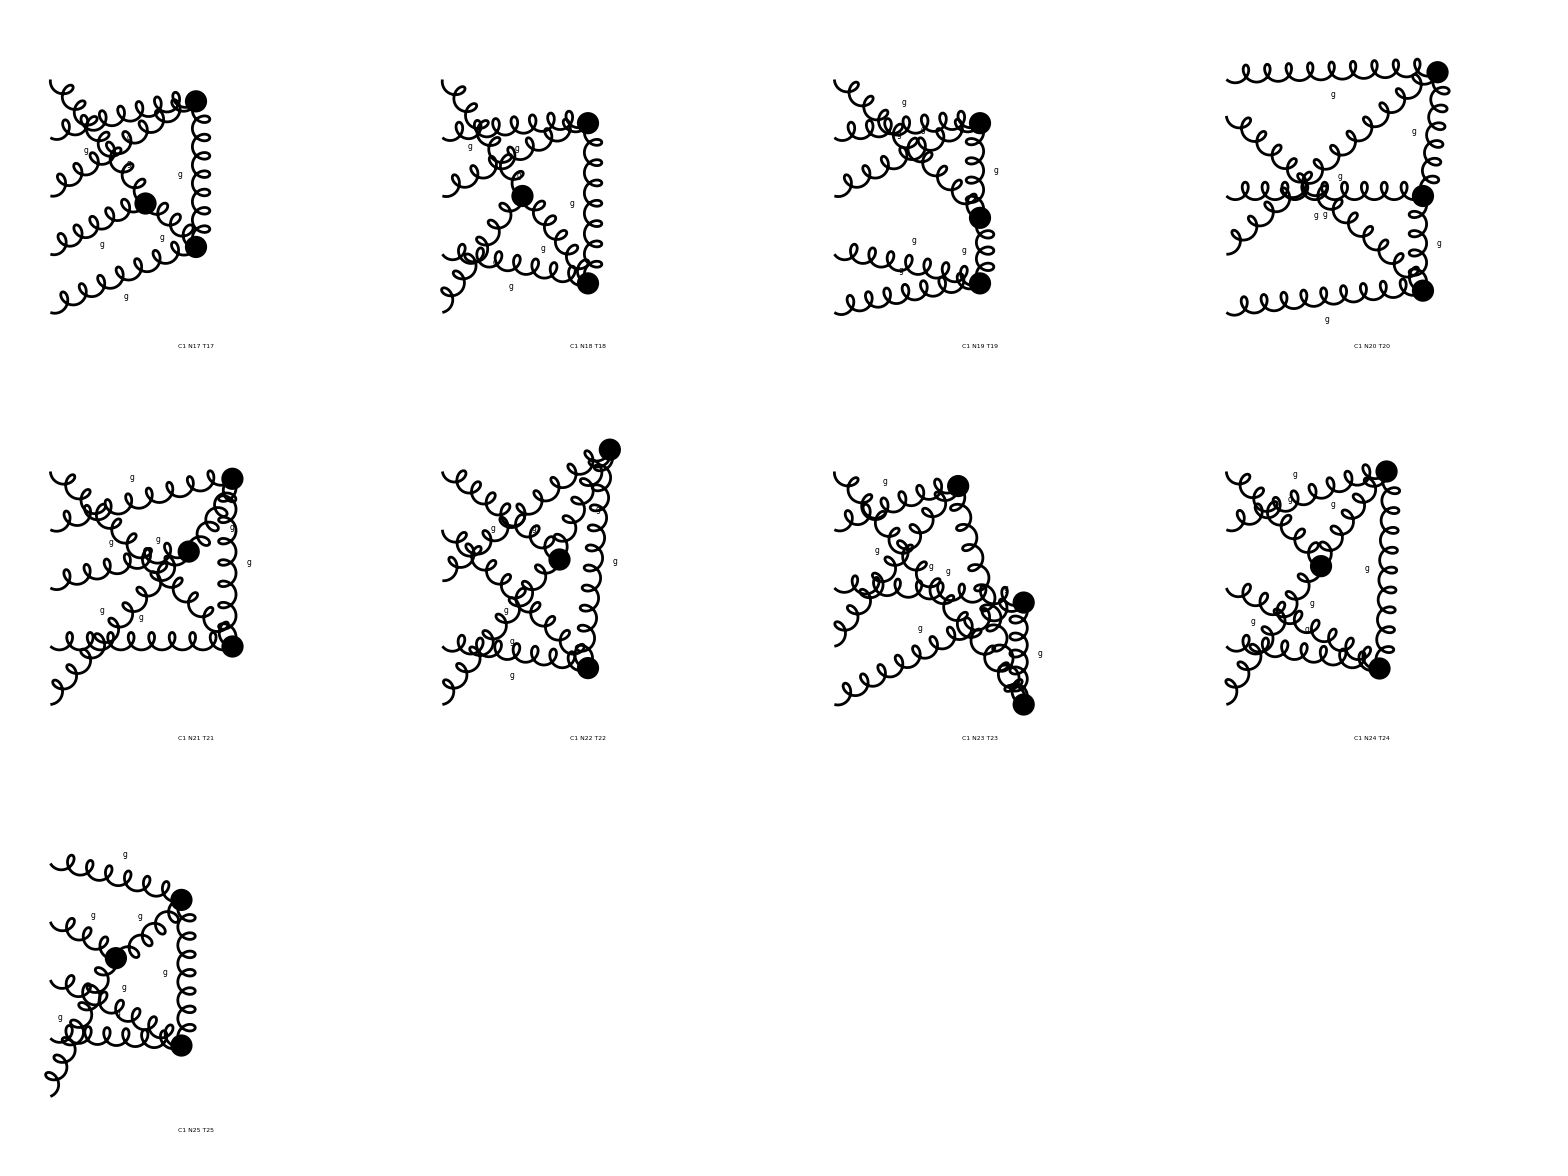

FeynArtsGraphics({g,g,g,g,g}→{})(([T1 C1 N1] | [T2 C1 N2] | [T3 C1 N3] | [T4 C1 N4]
[T5 C1 N5] | [T6 C1 N6] | [T7 C1 N7] | [T8 C1 N8]
[T9 C1 N9] | [T10 C1 N10] | [T11 C1 N11] | [T12 C1 N12]
[T13 C1 N13] | [T14 C1 N14] | [T15 C1 N15] | [T16 C1 N16]),([T17 C1 N17] | [T18 C1 N18] | [T19 C1 N19] | [T20 C1 N20]
[T21 C1 N21] | [T22 C1 N22] | [T23 C1 N23] | [T24 C1 N24]
[T25 C1 N25] | Null | Null | Null
Null | Null | Null | Null))

```mathematica
Paint[%,ColumnsXRows->4]
```

```mathematica
CreateFeynAmp[AA]
```

FeynAmpList(Process→(V(5,{Glu1}) | p1 | 0
V(5,{Glu2}) | p2 | 0
V(5,{Glu3}) | p3 | 0
V(5,{Glu4}) | p4 | 0
V(5,{Glu5}) | p5 | 0)→{},Model→SMQCD,GenericModel→Lorentz,AmplitudeLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==1)∫ⅆ^D Integral[](-g_s ((-(p1)+p2)_Lor6 g^Lor1Lor2+(p1-p3-p4-p5)_Lor2 g^Lor1Lor6+(-(p2)+p3+p4+p5)_Lor1 g^Lor2Lor6) g^Lor6Lor7 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(-(p3)-p4-p5)^2 SumOver(Glu6,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu2Glu6 (-ⅈ g^Lor3Lor7 g^Lor4Lor5 (-f_Glu3Glu4Glu5Glu6-f_Glu3Glu5Glu4Glu6) g_s^2-ⅈ g^Lor3Lor4 g^Lor5Lor7 (f_Glu3Glu5Glu4Glu6-f_Glu3Glu6Glu5Glu4) g_s^2-ⅈ g^Lor3Lor5 g^Lor4Lor7 (f_Glu3Glu4Glu5Glu6+f_Glu3Glu6Glu5Glu4) g_s^2)),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==2)∫ⅆ^D Integral[](-g_s ((-(p1)+p3)_Lor6 g^Lor1Lor3+(p1-p2-p4-p5)_Lor3 g^Lor1Lor6+(p2-p3+p4+p5)_Lor1 g^Lor3Lor6) g^Lor6Lor7 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(-(p2)-p4-p5)^2 SumOver(Glu6,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu3Glu6 (-ⅈ g^Lor2Lor7 g^Lor4Lor5 (-f_Glu2Glu4Glu5Glu6-f_Glu2Glu5Glu4Glu6) g_s^2-ⅈ g^Lor2Lor4 g^Lor5Lor7 (f_Glu2Glu5Glu4Glu6-f_Glu2Glu6Glu5Glu4) g_s^2-ⅈ g^Lor2Lor5 g^Lor4Lor7 (f_Glu2Glu4Glu5Glu6+f_Glu2Glu6Glu5Glu4) g_s^2)),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==3)∫ⅆ^D Integral[](-g_s ((-(p1)+p4)_Lor6 g^Lor1Lor4+(p1-p2-p3-p5)_Lor4 g^Lor1Lor6+(p2+p3-p4+p5)_Lor1 g^Lor4Lor6) g^Lor6Lor7 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(-(p2)-p3-p5)^2 SumOver(Glu6,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu4Glu6 (-ⅈ g^Lor2Lor7 g^Lor3Lor5 (-f_Glu2Glu3Glu5Glu6-f_Glu2Glu5Glu3Glu6) g_s^2-ⅈ g^Lor2Lor3 g^Lor5Lor7 (f_Glu2Glu5Glu3Glu6-f_Glu2Glu6Glu5Glu3) g_s^2-ⅈ g^Lor2Lor5 g^Lor3Lor7 (f_Glu2Glu3Glu5Glu6+f_Glu2Glu6Glu5Glu3) g_s^2)),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==4)∫ⅆ^D Integral[](-g_s ((-(p1)+p5)_Lor6 g^Lor1Lor5+(p1-p2-p3-p4)_Lor5 g^Lor1Lor6+(p2+p3+p4-p5)_Lor1 g^Lor5Lor6) g^Lor6Lor7 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(-(p2)-p3-p4)^2 SumOver(Glu6,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu5Glu6 (-ⅈ g^Lor2Lor7 g^Lor3Lor4 (-f_Glu2Glu3Glu4Glu6-f_Glu2Glu4Glu3Glu6) g_s^2-ⅈ g^Lor2Lor3 g^Lor4Lor7 (f_Glu2Glu4Glu3Glu6-f_Glu2Glu6Glu4Glu3) g_s^2-ⅈ g^Lor2Lor4 g^Lor3Lor7 (f_Glu2Glu3Glu4Glu6+f_Glu2Glu6Glu4Glu3) g_s^2)),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==5)∫ⅆ^D Integral[](-g_s ((-(p2)+p3)_Lor6 g^Lor2Lor3+(2 (p2)+p3)_Lor3 g^Lor2Lor6+(-(p2)-2 (p3))_Lor2 g^Lor3Lor6) g^Lor6Lor7 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(p2+p3)^2 SumOver(Glu6,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu2Glu3Glu6 (-ⅈ g^Lor1Lor7 g^Lor4Lor5 (-f_Glu1Glu4Glu5Glu6-f_Glu1Glu5Glu4Glu6) g_s^2-ⅈ g^Lor1Lor4 g^Lor5Lor7 (f_Glu1Glu5Glu4Glu6-f_Glu1Glu6Glu5Glu4) g_s^2-ⅈ g^Lor1Lor5 g^Lor4Lor7 (f_Glu1Glu4Glu5Glu6+f_Glu1Glu6Glu5Glu4) g_s^2)),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==6)∫ⅆ^D Integral[](-g_s ((-(p2)+p4)_Lor6 g^Lor2Lor4+(2 (p2)+p4)_Lor4 g^Lor2Lor6+(-(p2)-2 (p4))_Lor2 g^Lor4Lor6) g^Lor6Lor7 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(p2+p4)^2 SumOver(Glu6,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu2Glu4Glu6 (-ⅈ g^Lor1Lor7 g^Lor3Lor5 (-f_Glu1Glu3Glu5Glu6-f_Glu1Glu5Glu3Glu6) g_s^2-ⅈ g^Lor1Lor3 g^Lor5Lor7 (f_Glu1Glu5Glu3Glu6-f_Glu1Glu6Glu5Glu3) g_s^2-ⅈ g^Lor1Lor5 g^Lor3Lor7 (f_Glu1Glu3Glu5Glu6+f_Glu1Glu6Glu5Glu3) g_s^2)),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==7)∫ⅆ^D Integral[](-g_s ((-(p2)+p5)_Lor6 g^Lor2Lor5+(2 (p2)+p5)_Lor5 g^Lor2Lor6+(-(p2)-2 (p5))_Lor2 g^Lor5Lor6) g^Lor6Lor7 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(p2+p5)^2 SumOver(Glu6,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu2Glu5Glu6 (-ⅈ g^Lor1Lor7 g^Lor3Lor4 (-f_Glu1Glu3Glu4Glu6-f_Glu1Glu4Glu3Glu6) g_s^2-ⅈ g^Lor1Lor3 g^Lor4Lor7 (f_Glu1Glu4Glu3Glu6-f_Glu1Glu6Glu4Glu3) g_s^2-ⅈ g^Lor1Lor4 g^Lor3Lor7 (f_Glu1Glu3Glu4Glu6+f_Glu1Glu6Glu4Glu3) g_s^2)),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==8)∫ⅆ^D Integral[](-g_s ((-(p3)+p4)_Lor6 g^Lor3Lor4+(2 (p3)+p4)_Lor4 g^Lor3Lor6+(-(p3)-2 (p4))_Lor3 g^Lor4Lor6) g^Lor6Lor7 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(p3+p4)^2 SumOver(Glu6,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu3Glu4Glu6 (-ⅈ g^Lor1Lor7 g^Lor2Lor5 (-f_Glu1Glu2Glu5Glu6-f_Glu1Glu5Glu2Glu6) g_s^2-ⅈ g^Lor1Lor2 g^Lor5Lor7 (f_Glu1Glu5Glu2Glu6-f_Glu1Glu6Glu5Glu2) g_s^2-ⅈ g^Lor1Lor5 g^Lor2Lor7 (f_Glu1Glu2Glu5Glu6+f_Glu1Glu6Glu5Glu2) g_s^2)),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==9)∫ⅆ^D Integral[](-g_s ((-(p3)+p5)_Lor6 g^Lor3Lor5+(2 (p3)+p5)_Lor5 g^Lor3Lor6+(-(p3)-2 (p5))_Lor3 g^Lor5Lor6) g^Lor6Lor7 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(p3+p5)^2 SumOver(Glu6,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu3Glu5Glu6 (-ⅈ g^Lor1Lor7 g^Lor2Lor4 (-f_Glu1Glu2Glu4Glu6-f_Glu1Glu4Glu2Glu6) g_s^2-ⅈ g^Lor1Lor2 g^Lor4Lor7 (f_Glu1Glu4Glu2Glu6-f_Glu1Glu6Glu4Glu2) g_s^2-ⅈ g^Lor1Lor4 g^Lor2Lor7 (f_Glu1Glu2Glu4Glu6+f_Glu1Glu6Glu4Glu2) g_s^2)),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==10)∫ⅆ^D Integral[](-g_s ((-(p4)+p5)_Lor6 g^Lor4Lor5+(2 (p4)+p5)_Lor5 g^Lor4Lor6+(-(p4)-2 (p5))_Lor4 g^Lor5Lor6) g^Lor6Lor7 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(p4+p5)^2 SumOver(Glu6,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu4Glu5Glu6 (-ⅈ g^Lor1Lor7 g^Lor2Lor3 (-f_Glu1Glu2Glu3Glu6-f_Glu1Glu3Glu2Glu6) g_s^2-ⅈ g^Lor1Lor2 g^Lor3Lor7 (f_Glu1Glu3Glu2Glu6-f_Glu1Glu6Glu3Glu2) g_s^2-ⅈ g^Lor1Lor3 g^Lor2Lor7 (f_Glu1Glu2Glu3Glu6+f_Glu1Glu6Glu3Glu2) g_s^2)),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==11)∫ⅆ^D Integral[](ⅈ g_s^3 ((-(p1)+p2)_Lor6 g^Lor1Lor2+(p1-p3-p4-p5)_Lor2 g^Lor1Lor6+(-(p2)+p3+p4+p5)_Lor1 g^Lor2Lor6) ((-(p3)+p4)_Lor8 g^Lor3Lor4+(2 (p3)+p4)_Lor4 g^Lor3Lor8+(-(p3)-2 (p4))_Lor3 g^Lor4Lor8) g^Lor6Lor7 ((-(p3)-p4-2 (p5))_Lor9 g^Lor5Lor7+(-(p3)-p4+p5)_Lor7 g^Lor5Lor9+(2 (p3)+2 (p4)+p5)_Lor5 g^Lor7Lor9) g^Lor8Lor9 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(p3+p4)^2 1/(-(p3)-p4-p5)^2 SumOver(Glu6,8) SumOver(Glu7,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu2Glu6 f_Glu3Glu4Glu7 f_Glu5Glu6Glu7),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==12)∫ⅆ^D Integral[](ⅈ g_s^3 ((-(p1)+p2)_Lor6 g^Lor1Lor2+(p1-p3-p4-p5)_Lor2 g^Lor1Lor6+(-(p2)+p3+p4+p5)_Lor1 g^Lor2Lor6) ((-(p3)+p5)_Lor8 g^Lor3Lor5+(2 (p3)+p5)_Lor5 g^Lor3Lor8+(-(p3)-2 (p5))_Lor3 g^Lor5Lor8) g^Lor6Lor7 ((-(p3)-2 (p4)-p5)_Lor9 g^Lor4Lor7+(-(p3)+p4-p5)_Lor7 g^Lor4Lor9+(2 (p3)+p4+2 (p5))_Lor4 g^Lor7Lor9) g^Lor8Lor9 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(-(p3)-p4-p5)^2 1/(p3+p5)^2 SumOver(Glu6,8) SumOver(Glu7,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu2Glu6 f_Glu3Glu5Glu7 f_Glu4Glu6Glu7),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==13)∫ⅆ^D Integral[](ⅈ g_s^3 ((-(p1)+p2)_Lor6 g^Lor1Lor2+(p1-p3-p4-p5)_Lor2 g^Lor1Lor6+(-(p2)+p3+p4+p5)_Lor1 g^Lor2Lor6) ((-(p4)+p5)_Lor9 g^Lor4Lor5+(2 (p4)+p5)_Lor5 g^Lor4Lor9+(-(p4)-2 (p5))_Lor4 g^Lor5Lor9) g^Lor6Lor7 ((-2 (p3)-p4-p5)_Lor8 g^Lor3Lor7+(p3-p4-p5)_Lor7 g^Lor3Lor8+(p3+2 (p4)+2 (p5))_Lor3 g^Lor7Lor8) g^Lor8Lor9 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(-(p4)-p5)^2 1/(-(p3)-p4-p5)^2 SumOver(Glu6,8) SumOver(Glu7,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu2Glu6 f_Glu3Glu6Glu7 f_Glu4Glu5Glu7),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==14)∫ⅆ^D Integral[](ⅈ g_s^3 ((-(p1)+p3)_Lor6 g^Lor1Lor3+(p1-p2-p4-p5)_Lor3 g^Lor1Lor6+(p2-p3+p4+p5)_Lor1 g^Lor3Lor6) ((-(p2)+p4)_Lor8 g^Lor2Lor4+(2 (p2)+p4)_Lor4 g^Lor2Lor8+(-(p2)-2 (p4))_Lor2 g^Lor4Lor8) g^Lor6Lor7 ((-(p2)-p4-2 (p5))_Lor9 g^Lor5Lor7+(-(p2)-p4+p5)_Lor7 g^Lor5Lor9+(2 (p2)+2 (p4)+p5)_Lor5 g^Lor7Lor9) g^Lor8Lor9 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(p2+p4)^2 1/(-(p2)-p4-p5)^2 SumOver(Glu6,8) SumOver(Glu7,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu3Glu6 f_Glu2Glu4Glu7 f_Glu5Glu6Glu7),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==15)∫ⅆ^D Integral[](ⅈ g_s^3 ((-(p1)+p3)_Lor6 g^Lor1Lor3+(p1-p2-p4-p5)_Lor3 g^Lor1Lor6+(p2-p3+p4+p5)_Lor1 g^Lor3Lor6) ((-(p2)+p5)_Lor8 g^Lor2Lor5+(2 (p2)+p5)_Lor5 g^Lor2Lor8+(-(p2)-2 (p5))_Lor2 g^Lor5Lor8) g^Lor6Lor7 ((-(p2)-2 (p4)-p5)_Lor9 g^Lor4Lor7+(-(p2)+p4-p5)_Lor7 g^Lor4Lor9+(2 (p2)+p4+2 (p5))_Lor4 g^Lor7Lor9) g^Lor8Lor9 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(-(p2)-p4-p5)^2 1/(p2+p5)^2 SumOver(Glu6,8) SumOver(Glu7,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu3Glu6 f_Glu2Glu5Glu7 f_Glu4Glu6Glu7),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==16)∫ⅆ^D Integral[](ⅈ g_s^3 ((-(p1)+p3)_Lor6 g^Lor1Lor3+(p1-p2-p4-p5)_Lor3 g^Lor1Lor6+(p2-p3+p4+p5)_Lor1 g^Lor3Lor6) ((-(p4)+p5)_Lor9 g^Lor4Lor5+(2 (p4)+p5)_Lor5 g^Lor4Lor9+(-(p4)-2 (p5))_Lor4 g^Lor5Lor9) g^Lor6Lor7 ((-2 (p2)-p4-p5)_Lor8 g^Lor2Lor7+(p2-p4-p5)_Lor7 g^Lor2Lor8+(p2+2 (p4)+2 (p5))_Lor2 g^Lor7Lor8) g^Lor8Lor9 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(-(p4)-p5)^2 1/(-(p2)-p4-p5)^2 SumOver(Glu6,8) SumOver(Glu7,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu3Glu6 f_Glu2Glu6Glu7 f_Glu4Glu5Glu7),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==17)∫ⅆ^D Integral[](ⅈ g_s^3 ((-(p2)+p3)_Lor8 g^Lor2Lor3+(2 (p2)+p3)_Lor3 g^Lor2Lor8+(-(p2)-2 (p3))_Lor2 g^Lor3Lor8) ((-(p1)+p4)_Lor6 g^Lor1Lor4+(p1-p2-p3-p5)_Lor4 g^Lor1Lor6+(p2+p3-p4+p5)_Lor1 g^Lor4Lor6) g^Lor6Lor7 ((-(p2)-p3-2 (p5))_Lor9 g^Lor5Lor7+(-(p2)-p3+p5)_Lor7 g^Lor5Lor9+(2 (p2)+2 (p3)+p5)_Lor5 g^Lor7Lor9) g^Lor8Lor9 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(p2+p3)^2 1/(-(p2)-p3-p5)^2 SumOver(Glu6,8) SumOver(Glu7,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu4Glu6 f_Glu2Glu3Glu7 f_Glu5Glu6Glu7),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==18)∫ⅆ^D Integral[](ⅈ g_s^3 ((-(p2)+p3)_Lor8 g^Lor2Lor3+(2 (p2)+p3)_Lor3 g^Lor2Lor8+(-(p2)-2 (p3))_Lor2 g^Lor3Lor8) ((-(p1)+p5)_Lor6 g^Lor1Lor5+(p1-p2-p3-p4)_Lor5 g^Lor1Lor6+(p2+p3+p4-p5)_Lor1 g^Lor5Lor6) g^Lor6Lor7 ((-(p2)-p3-2 (p4))_Lor9 g^Lor4Lor7+(-(p2)-p3+p4)_Lor7 g^Lor4Lor9+(2 (p2)+2 (p3)+p4)_Lor4 g^Lor7Lor9) g^Lor8Lor9 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(p2+p3)^2 1/(-(p2)-p3-p4)^2 SumOver(Glu6,8) SumOver(Glu7,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu5Glu6 f_Glu2Glu3Glu7 f_Glu4Glu6Glu7),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==19)∫ⅆ^D Integral[](ⅈ g_s^3 ((-(p2)+p3)_Lor7 g^Lor2Lor3+(2 (p2)+p3)_Lor3 g^Lor2Lor7+(-(p2)-2 (p3))_Lor2 g^Lor3Lor7) ((-(p4)+p5)_Lor9 g^Lor4Lor5+(2 (p4)+p5)_Lor5 g^Lor4Lor9+(-(p4)-2 (p5))_Lor4 g^Lor5Lor9) g^Lor6Lor7 ((-(p1)+p2+p3)_Lor8 g^Lor1Lor6+(p1-p4-p5)_Lor6 g^Lor1Lor8+(-(p2)-p3+p4+p5)_Lor1 g^Lor6Lor8) g^Lor8Lor9 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(-(p2)-p3)^2 1/(-(p4)-p5)^2 SumOver(Glu6,8) SumOver(Glu7,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu6Glu7 f_Glu2Glu3Glu6 f_Glu4Glu5Glu7),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==20)∫ⅆ^D Integral[](ⅈ g_s^3 ((-(p1)+p4)_Lor6 g^Lor1Lor4+(p1-p2-p3-p5)_Lor4 g^Lor1Lor6+(p2+p3-p4+p5)_Lor1 g^Lor4Lor6) ((-(p2)+p5)_Lor8 g^Lor2Lor5+(2 (p2)+p5)_Lor5 g^Lor2Lor8+(-(p2)-2 (p5))_Lor2 g^Lor5Lor8) g^Lor6Lor7 ((-(p2)-2 (p3)-p5)_Lor9 g^Lor3Lor7+(-(p2)+p3-p5)_Lor7 g^Lor3Lor9+(2 (p2)+p3+2 (p5))_Lor3 g^Lor7Lor9) g^Lor8Lor9 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(-(p2)-p3-p5)^2 1/(p2+p5)^2 SumOver(Glu6,8) SumOver(Glu7,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu4Glu6 f_Glu2Glu5Glu7 f_Glu3Glu6Glu7),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==21)∫ⅆ^D Integral[](ⅈ g_s^3 ((-(p1)+p4)_Lor6 g^Lor1Lor4+(p1-p2-p3-p5)_Lor4 g^Lor1Lor6+(p2+p3-p4+p5)_Lor1 g^Lor4Lor6) ((-(p3)+p5)_Lor9 g^Lor3Lor5+(2 (p3)+p5)_Lor5 g^Lor3Lor9+(-(p3)-2 (p5))_Lor3 g^Lor5Lor9) g^Lor6Lor7 ((-2 (p2)-p3-p5)_Lor8 g^Lor2Lor7+(p2-p3-p5)_Lor7 g^Lor2Lor8+(p2+2 (p3)+2 (p5))_Lor2 g^Lor7Lor8) g^Lor8Lor9 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(-(p3)-p5)^2 1/(-(p2)-p3-p5)^2 SumOver(Glu6,8) SumOver(Glu7,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu4Glu6 f_Glu2Glu6Glu7 f_Glu3Glu5Glu7),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==22)∫ⅆ^D Integral[](ⅈ g_s^3 ((-(p2)+p4)_Lor8 g^Lor2Lor4+(2 (p2)+p4)_Lor4 g^Lor2Lor8+(-(p2)-2 (p4))_Lor2 g^Lor4Lor8) ((-(p1)+p5)_Lor6 g^Lor1Lor5+(p1-p2-p3-p4)_Lor5 g^Lor1Lor6+(p2+p3+p4-p5)_Lor1 g^Lor5Lor6) g^Lor6Lor7 ((-(p2)-2 (p3)-p4)_Lor9 g^Lor3Lor7+(-(p2)+p3-p4)_Lor7 g^Lor3Lor9+(2 (p2)+p3+2 (p4))_Lor3 g^Lor7Lor9) g^Lor8Lor9 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(-(p2)-p3-p4)^2 1/(p2+p4)^2 SumOver(Glu6,8) SumOver(Glu7,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu5Glu6 f_Glu2Glu4Glu7 f_Glu3Glu6Glu7),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==23)∫ⅆ^D Integral[](ⅈ g_s^3 ((-(p2)+p4)_Lor7 g^Lor2Lor4+(2 (p2)+p4)_Lor4 g^Lor2Lor7+(-(p2)-2 (p4))_Lor2 g^Lor4Lor7) ((-(p3)+p5)_Lor9 g^Lor3Lor5+(2 (p3)+p5)_Lor5 g^Lor3Lor9+(-(p3)-2 (p5))_Lor3 g^Lor5Lor9) g^Lor6Lor7 ((-(p1)+p2+p4)_Lor8 g^Lor1Lor6+(p1-p3-p5)_Lor6 g^Lor1Lor8+(-(p2)+p3-p4+p5)_Lor1 g^Lor6Lor8) g^Lor8Lor9 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(-(p2)-p4)^2 1/(-(p3)-p5)^2 SumOver(Glu6,8) SumOver(Glu7,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu6Glu7 f_Glu2Glu4Glu6 f_Glu3Glu5Glu7),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==24)∫ⅆ^D Integral[](ⅈ g_s^3 ((-(p3)+p4)_Lor9 g^Lor3Lor4+(2 (p3)+p4)_Lor4 g^Lor3Lor9+(-(p3)-2 (p4))_Lor3 g^Lor4Lor9) ((-(p1)+p5)_Lor6 g^Lor1Lor5+(p1-p2-p3-p4)_Lor5 g^Lor1Lor6+(p2+p3+p4-p5)_Lor1 g^Lor5Lor6) g^Lor6Lor7 ((-2 (p2)-p3-p4)_Lor8 g^Lor2Lor7+(p2-p3-p4)_Lor7 g^Lor2Lor8+(p2+2 (p3)+2 (p4))_Lor2 g^Lor7Lor8) g^Lor8Lor9 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(-(p3)-p4)^2 1/(-(p2)-p3-p4)^2 SumOver(Glu6,8) SumOver(Glu7,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu5Glu6 f_Glu2Glu6Glu7 f_Glu3Glu4Glu7),∫ⅆ^D GraphID(Topology==1,Generic==1,Classes==1,Number==25)∫ⅆ^D Integral[](ⅈ g_s^3 ((-(p3)+p4)_Lor9 g^Lor3Lor4+(2 (p3)+p4)_Lor4 g^Lor3Lor9+(-(p3)-2 (p4))_Lor3 g^Lor4Lor9) ((-(p2)+p5)_Lor7 g^Lor2Lor5+(2 (p2)+p5)_Lor5 g^Lor2Lor7+(-(p2)-2 (p5))_Lor2 g^Lor5Lor7) g^Lor6Lor7 ((-(p1)+p2+p5)_Lor8 g^Lor1Lor6+(p1-p3-p4)_Lor6 g^Lor1Lor8+(-(p2)+p3+p4-p5)_Lor1 g^Lor6Lor8) g^Lor8Lor9 ep(V(5,{Glu1}),p1,Lor1) ep(V(5,{Glu2}),p2,Lor2) ep(V(5,{Glu3}),p3,Lor3) ep(V(5,{Glu4}),p4,Lor4) ep(V(5,{Glu5}),p5,Lor5) 1/(-(p3)-p4)^2 1/(-(p2)-p5)^2 SumOver(Glu6,8) SumOver(Glu7,8) SumOver(Glu1,8,External) SumOver(Glu2,8,External) SumOver(Glu3,8,External) SumOver(Glu4,8,External) SumOver(Glu5,8,External) f_Glu1Glu6Glu7 f_Glu2Glu5Glu6 f_Glu3Glu4Glu7))